```mathematica
(*Practica 2.1 CMC 
I- Fundamentos Básicos

Ángel Carrascosa Beltrán
  Laura Ruiz Muñoz*)
```

```mathematica
Regla[num_Integer] :=Module[{res,aux,fin,i},
res={{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};
aux =num;
fin=False;
For[i=1,i≤Length[res],i++,
If[fin==True,res[[i]]=Insert[res[[i]],0,4];];
If[aux==1, aux=0;fin =True;res[[i]]=Insert[res[[i]],1,4];];
If[aux>1,
If[Divisible[aux,2],
res[[i]]=Insert[res[[i]],0,4];
,(*else*)
res[[i]]=Insert[res[[i]],1,4];
aux--;
];
aux=aux/2;
];
];
Return[res];
];
Regla[54]

NextTransition[trans0_List,rule_List]:=Module[{transAct,transRes,cellNeigborhood,i},
transRes={};
transAct=Append[trans0,trans0[[1]]];
transAct=Prepend[transAct,trans0[[Length[trans0]]]];
For[i=2,i<Length[transAct],i++,
cellNeigborhood={transAct[[i-1]],transAct[[i]],transAct[[i+1]],_};
transRes=Append[transRes,Cases[rule,cellNeigborhood][[1]][[4]]];
];
Return[transRes];
];
NextTransition[{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1},{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,1},{1,1,0,0},{1,1,1,0}}]
```

{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,1},{1,1,0,0},{1,1,1,0}}

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0}

```mathematica
AC[Inicial_List,ReglaNum_Integer,t_Integer]:=Module[{transitions,ruleList,i},
If[ReglaNum<0 || ReglaNum>255,
Print["Rule number (ReglaNum_) is outside range (0,255)"];
Return[-3];
];
If[Length[Inicial]<1,
Print["Automata initial list (Inicial_) is empty"];
Return[-2];
];
transitions={Inicial};
ruleList=Regla[ReglaNum];
For [i=1,i≤t,i++,
transitions=Append[transitions,NextTransition[transitions[[Length[transitions]]],ruleList]];
];
ArrayPlot[transitions]
];
```

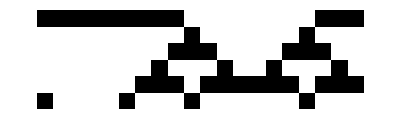

-Graphics-

```mathematica
AC[{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1},54,5]


ArrayPlot[CellularAutomaton[54,{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1},5]]
```